(I)
Answer 1
e^x is not the syntax of Mathematica, the following needs to be written:

ⅇ^x

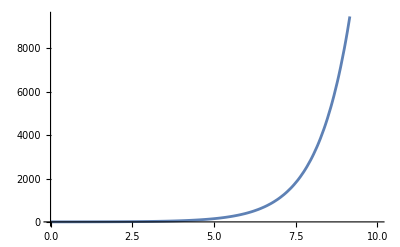

```mathematica
f[x_]=Exp[x] (*Code to Plot exponential function*)
Plot[f[x],{x,0,10}]
```

Answer 2
Syntax for sine wave is not sin {x}
The range of x should be put in braces, not parentheses.
The initial of Plot must be in uppercase.
x_ should be the argument of g while defining it, not x.

Sin[x]

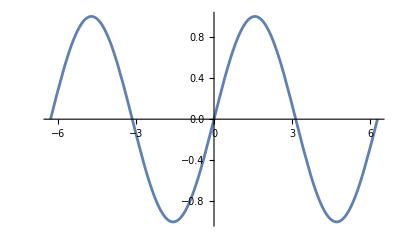

```mathematica
g[x_]=Sin[x] (*Code to Plot a sine function*)
Plot[g[x],{x,-2 Pi,2 Pi}]
```

Answer 3
The square bracket needs to be removed
variable is t, not x

{t→0.876726}

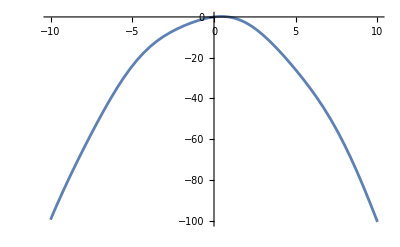

```mathematica
FindRoot[Sin[t]-t^2,{t,1}] (*Finding the root of f(t)=Sin(t)-t^2*)
Plot[Sin[t]-t^2,{t,-10,10}]
```

Answer 4
Correct use of brackets has to be done, range of x is from {0,10}

```mathematica
Manipulate[Plot[{x^n,x+n,√((x n)/7)},{x,0,10}],{{n,0},10,15}]
```

Answer 5

Piecewise[{{x^2, x<0}, {x, x≥0}, {0, True}}]

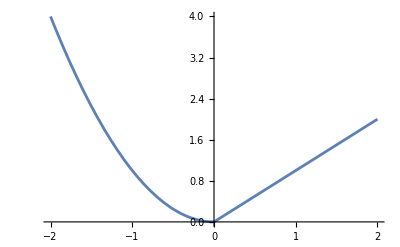

```mathematica
k=Piecewise[{{x^2,x<0},{x,x≥0}}]
Plot[k,{x,-2,2}]
(*Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]*)
```

(II) Arranged in the order of  a increasing growth rate

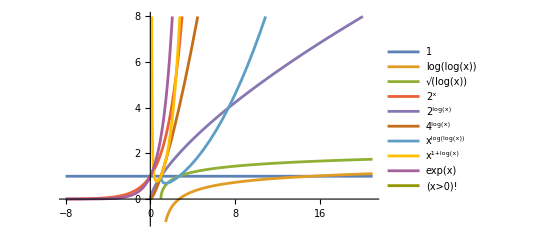

```mathematica
Plot[{1,Log[Log[x]],Sqrt[Log[x]],2^x,2^Log[x],4^Log[x],x^(Log[Log[x]]),x^(1+Log[x]),Exp[x],Factorial[x>0]},{x,-8,21},PlotRange->{-1,8},PlotLegends->"Expressions"]
```

(III) Taylor Expansion

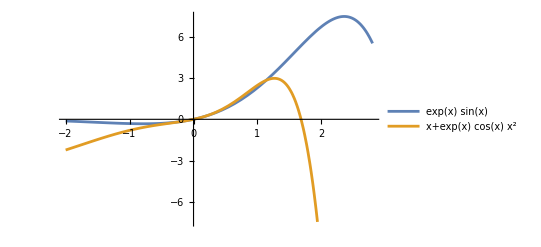

```mathematica
Plot[{Exp[x]Sin[x],x+Exp[x] Cos[x] x^2},{x,-2,2.8},PlotLegends->"Expressions"]
```

(IV)N[x]

```mathematica
(*a*)N[Pi]
	   N[Pi,10]
	   N[E,10]
(*b*)N[Pi,100]
(*c*)N[2^(1/2) ,16]
	   N[2^(1/3),16]
```

3.14159

3.141592654

2.718281828

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

1.414213562373095

1.259921049894873

(V) Analysing distance between consecutive minima

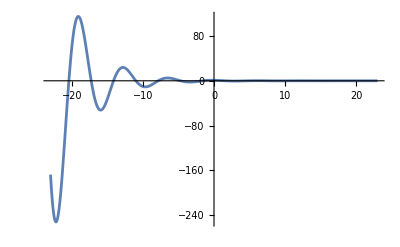

{{x→2.89661},{x→-0.244979}}

Positive second derivative means minimum:

0.499653

-1.09588

```mathematica
Plot[Exp[-x/4] Cos[x],{x,-23,23},PlotRange->Full]
sol=Solve[D[Exp[-x/4] Cos[x],x]==0,x]//N
Print["Positive second derivative means minimum:"]
a=D[Exp[-x/4] Cos[x],{x,2}]/.sol[[1]]
b=D[Exp[-x/4] Cos[x],{x,2}]/.sol[[2]]
```

(VI)

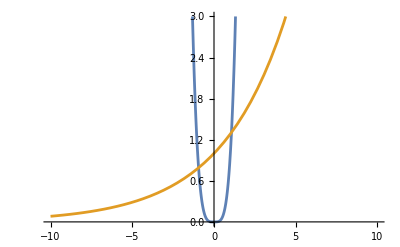

```mathematica
Plot[{x^4,Exp[x/4]},{x,-10,10},PlotRange->{0,3}]
```

```mathematica
Solve[x^4==Exp[x/4],x,Reals]//N
(*What more should we do to get the y value as well?*)
```

{{x→1.0691},{x→-0.942779},{x→67.3611}}

(VII)

```mathematica
Plot[{Sin[9 t]^2,Cos[81 t],Sin[9 t] Cos[9 t]},{t,-2 Pi/9,2 Pi/9},PlotLabels->Automatic]
```

-Graphics-